## Pendulum swing up, robust feedforward vs. feedback (Section 9.1.2)

```mathematica
Clear["Global`*"];
ωnom=1;n=500;  τ=5;τ1=8;
```

```mathematica
ffNom[n_,τ_]:=Module[{f,x1,x2,λ2,λ1,t,Δt,bcs,eqns,sv,froot,x1ff0,x2ff0,uff0,x1ff,x2ff,uff},
Δt=τ/n;
f[{x1_,x2_,λ1_,λ2_}] := {x2,-Sin[x1]-λ2,Cos[x1]λ2,-λ1};
bcs={Subscript[x1, 0]==0,Subscript[x2, 0]==0,Subscript[x1, n]==π,Subscript[x2, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[x1, i],Subscript[x2, i],Subscript[λ1, i],Subscript[λ2, i]}== {Subscript[x1, i-1],Subscript[x2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1]}
+Δt/2(f[{Subscript[x1, i-1],Subscript[x2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1]}]+f[{Subscript[x1, i],Subscript[x2, i],Subscript[λ1, i],Subscript[λ2, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[x1, i],0},{Subscript[x2, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

x1ff0=ListInterpolation[Table[Subscript[x1, i],{i,0,n}]/.froot,{0,τ}];
x2ff0=ListInterpolation[Table[Subscript[x2, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ2, i],{i,0,n}]/.froot,{0,τ}];

x1ff[t_]:=Piecewise[{{x1ff0[t],0≤t≤τ}},π];
x2ff[t_]:=Piecewise[{{x2ff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{x1ff,x2ff,uff}]

{θnom,θdotnom,unom}=ffNom[n,τ];
```

Test the approximate solution on ff for different frequencies ω.  Add local linear feedback.

```mathematica
SwingUpFB[τ_,τ1_,θff_,θdotff_,uff_,ω_]:=Module[{eq,init,θ,θdot,θs,θdots,us,t,Jτ,κ1,κ2,ufb,u},
κ1=κ2=(√2+1);  (* lqr for q=r for balancing pendulum *)
ufb[t_]:=κ1(θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t]);
u[t_]:=uff[t]+ufb[t];
eq={θ'[t]==θdot[t],θdot'[t]==-ω^2 Sin[θ[t]]+u[t]};
init={θ[0]==θdot[0]==0};
{θs,θdots}=NDSolveValue[{eq,init},{θ,θdot},{t,0,τ1}];
us[t_]:=uff[t]+κ1(θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t]);
Jτ=1/2((θs[τ]-π)^2+θdots[τ]^2);
{θs,us,Jτ}]
```

Design robust feedforward for nominal ω = 1

```mathematica
ffRob[n_,τ_]:=Module[{f,x1,x2,xω1,xω2,λ1,λ2,λω1,λω2,t,Δt,bcs,eqns,sv,froot,x1ff0,x2ff0,uff0,xω1ff0,xω2ff0,x1ff,x2ff,uff},
Δt=τ/n;
f[{x1_,x2_,xω1_,xω2_,λ1_,λ2_,λω1_,λω2_}] := {x2,-Sin[x1]-λ2,xω2,-2Sin[x1]-Cos[x1]xω1,Cos[x1]λ2+(2Cos[x1]-Sin[x1]xω1)λω2,-λ1,Cos[x1]λω2,-λω1};
(*  GOT THIS FAR!! *)
bcs={Subscript[x1, 0]==0,Subscript[x2, 0]==0,Subscript[xω1, 0]==0,Subscript[xω2, 0]==0,Subscript[x1, n]==π,Subscript[x2, n]==0,Subscript[xω1, n]==0,Subscript[xω2, n]==0}; (* hard final constraint *)
eqns=Flatten[Join[bcs,
Table[Thread[{Subscript[x1, i],Subscript[x2, i],Subscript[xω1, i],Subscript[xω2, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λω1, i],Subscript[λω2, i]}== {Subscript[x1, i-1],Subscript[x2, i-1],Subscript[xω1, i-1],Subscript[xω2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λω1, i-1],Subscript[λω2, i-1]}
+Δt/2(f[{Subscript[x1, i-1],Subscript[x2, i-1],Subscript[xω1, i-1],Subscript[xω2, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λω1, i-1],Subscript[λω2, i-1]}]+f[{Subscript[x1, i],Subscript[x2, i],Subscript[xω1, i],Subscript[xω2, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λω1, i],Subscript[λω2, i]}])],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[x1, i],0i Δt},{Subscript[x2, i],0},{Subscript[xω1, i],0},{Subscript[xω2, i],0},{Subscript[λ1, i],0},{Subscript[λ2, i],0},{Subscript[λω1, i],0},{Subscript[λω2, i],0}},{i,0,n}],1];
	(* initial guesses = 0, very naive! *)
froot=FindRoot[eqns,sv];

x1ff0=ListInterpolation[Table[Subscript[x1, i],{i,0,n}]/.froot,{0,τ}];
x2ff0=ListInterpolation[Table[Subscript[x2, i],{i,0,n}]/.froot,{0,τ}];
uff0=ListInterpolation[Table[-Subscript[λ2, i],{i,0,n}]/.froot,{0,τ}];
xω1ff0=ListInterpolation[Table[Subscript[xω1, i],{i,0,n}]/.froot,{0,τ}];
xω2ff0=ListInterpolation[Table[Subscript[xω2, i],{i,0,n}]/.froot,{0,τ}];

x1ff[t_]:=Piecewise[{{x1ff0[t],0≤t≤τ}},π];
x2ff[t_]:=Piecewise[{{x2ff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
{x1ff,x2ff,uff,xω1ff0,xω2ff0}]

{θrob,θdotrob,urob,xω1rob,xω2rob}=ffRob[n,τ];
```

Evaluate nominal & robust feedforward controls u(t) for different frequencies ω

```mathematica
ϵ=0.1;
{θ1,u1,J1}=SwingUpFB[τ,τ1,θnom,θdotnom,unom,ωnom];
{θ1a,u1a,J1a}=SwingUpFB[τ,τ1,θnom,θdotnom,unom,ωnom-ϵ];
{θ1b,u1b,J1b}=SwingUpFB[τ,τ1,θnom,θdotnom,unom,ωnom+ϵ];

{θ2,u2,J2}=SwingUpFB[τ,τ1,θrob,θdotrob,urob,ωnom];
{θ2a,u2a,J2a}=SwingUpFB[τ,τ1,θrob,θdotrob,urob,ωnom-ϵ];
{θ2b,u2b,J2b}=SwingUpFB[τ,τ1,θrob,θdotrob,urob,ωnom+ϵ];
```

InterpolatingFunction::dmval: Input value {5.00127} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.01268} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.0134} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.0202} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.03262} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.04737} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

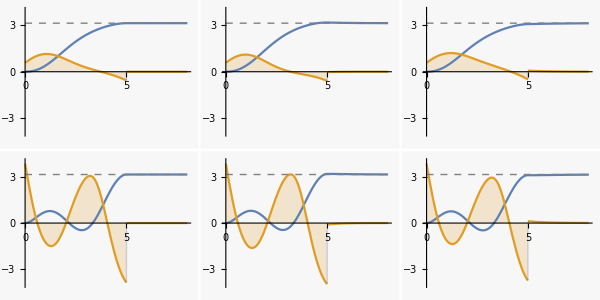

```mathematica
Plotit[θ_,u_,τ_]:= Plot[{θ[t],u[t],π},{t,0,τ},PlotStyle->{,,Directive[Gray,Dashed,Thin]},PlotRange->{-4,4},Filling->{2->Axis}]

p1=Plotit[θ1,u1,τ1];   (* nominal algorithm *)
p1a=Plotit[θ1a,u1a,τ1];p1b=Plotit[θ1b,u1b,τ1];

p2=Plotit[θ2,u2,τ1];   (* robust algorithm *)
p2a=Plotit[θ2a,u2a,τ1];p2b=Plotit[θ2b,u2b,τ1];

GraphicsGrid[{{p1,p1a,p1b},{p2,p2a,p2b}},Spacings->4,ImageSize->{600,300}]
```

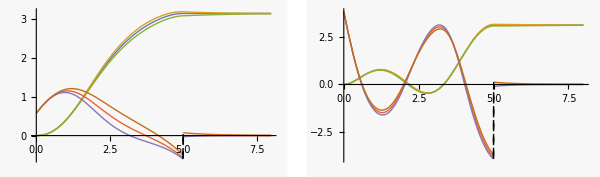

```mathematica
GraphicsRow[{Plot[{θ1[t],θ1a[t],θ1b[t],unom[t],u1a[t],u1b[t]},{t,0,τ1}],Plot[{θ2[t],θ2a[t],θ2b[t],urob[t],u2a[t],u2b[t]},{t,0,τ1}]},ImageSize->600]
```

```mathematica
GetJu[u_,τ_]:=1/2 NIntegrate[u[t]^2,{t,0,τ}];Ju1=GetJu[u1,τ1];Ju1a=GetJu[u1a,τ1];Ju1b=GetJu[u1b,τ1];
Ju2=GetJu[u2,τ1]; Ju2a=GetJu[u2a,τ1]; Ju2b=GetJu[u2b,τ1];{Ju1,Ju1a,Ju1b,Ju2,Ju2a,Ju2b}
```

{1.21259,1.03456,1.51387,9.87536,10.5684,9.14644}

Reality check:  what happens when you just use feedback?

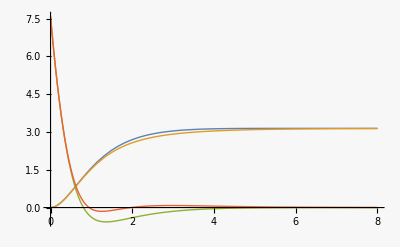

```mathematica
θnone[t_]:=π; θdotnone[t_]:=0;  (* setpoint = vertical equilibrium *)
unone[t_]:=0;   (* no feedforward.  Use zero function *)

{θ0,u0,J0}=SwingUpFB[τ,τ1,θnone,θdotnone,unone,ωnom];
{θ0a,u0a,J0a}=SwingUpFB[τ,τ1,θnone,θdotnone,unone,ωnom-ϵ];
{θ0b,u0b,J0b}=SwingUpFB[τ,τ1,θnone,θdotnone,unone,ωnom+ϵ];
Ju0=GetJu[u0,τ1];Ju0a=GetJu[u0a,τ1];Ju0b=GetJu[u0b,τ1];

Plot[{θ0a[t],θ0b[t],u0a[t],u0b[t]},{t,0,τ1}]
```

Here:  the actuator is so strong that linear feedback still works.  It would be more realistic to limit the u_max so that direct torque is not enough (on a static pendulum).  This would make the linear controller fail.

Export data

```mathematica
dt=0.05;dat=Table[Through[{θ1,θ1a,θ1b,u1,u1a,u1b,θ2,θ2a,θ2b,u2,u2a,u2b}[t]],{t,0,τ1,dt}]//N;
(* 
SetDirectory[NotebookDirectory[]];
Export["pendFFvFB.dat", dat]; 
*)
```